Finite element models of multiphysics problems
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 20 December 2021 - Contact: m.marino@ing.uniroma2.it

# Elements

## Q1CEind - Chemical diffusion and Mechanics (independent fields)

### Initialization

```mathematica
<<AceGen`;
SMSInitialize["Q1CEind","Environment"->"AceFEM"];
SMSTemplate[
"SMSTopology"->"Q1",
(*Add four nodes for pressure variable*)
"SMSNoNodes"->8,
(*DOF for each node*)
"SMSDOFGlobal"->{2,2,2,2,1,1,1,1},
(*ID of each node*)
"SMSNodeID"->{"D","D","D","D","c","c","c","c"},
(*Location of additional node*)
"SMSAdditionalNodes"->Function[{x1,x2,x3,x4},{x1,x2,x3,x4}],
(*Domain Data (Material) parameters*)
"SMSDomainDataNames"->{"E -elastic modulus","ν -poisson ratio",
"kc -flux constant","ceq -equilibrium concentration","μo -reference potential",
"Dc -diffusivity constant","m -mobility parameter"},
"SMSDefaultData"->{1,0.3,1,1,0,1,1}
];

RelevantNumbers[]:=(
nen=SMSNoNodes;
nenX=4;
nenU=4;
ndim=SMSNoDimensions;
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
)
```

### Element Definitions

```mathematica
ElementDefinitions[Ig_]:=(

(*MATERIAL AND ELEMENT DATA*)
{Ee,ν,kc,ceq,μo,Dc,m}⊨SMSIO["Domain data"];
RT⊨Dc/m;

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕡eIO}⊨SMSIO["All coordinates and DOFs"];
𝕡e=Flatten[𝕡eIO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
ℕh⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nenU}];

(*ISOPARAMETRIC MAPPING*)
𝕏IOgeo⊨𝕏IO⟦1;;nenX⟧;
𝕏⊨SMSFreeze[ℕh.𝕏IOgeo];
𝕁e⊨SMSD[𝕏,{ξ,η}];
Jed⊨SMSDet[𝕁e];

(*CURRENT TIME-STEP QUANTITIES: KINEMATICS AND CONCENTRATION*)
𝕦IO⊨𝕡eIO⟦1;;nenU⟧;
𝕦⊨ℕh.𝕦IO;
ℍ⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[ϵ,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];
(**)
cIO⊨𝕡eIO⟦nenU+1;;nen,1⟧;
c⊨SMSFreeze[ceq+ℕh.cIO];
Gradc⊨SMSD[c,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];

(*PREVIOUS TIME-STEP QUANTITIES: CONCENTRATION*)
𝕡enIO⊨SMSIO["Nodal DOFs n"];
(**)
cnIO⊨𝕡enIO⟦nenU+1;;nen,1⟧;
cn⊨ceq+ℕh.cnIO;

(*DISCRETE TIME DERIVATIVE*)
Δt⊨SMSReal[rdata$$["TimeIncrement"]];
DcDt⊨(c-cn)/Δt;

(*ELASTIC ENERGY*)
{G,K}⊨SMSHookeToBulk[Ee,ν];
Ψel⊨1/2 (K-2/3 G)(Tr[ϵ])^2+G Tr[Transpose[ϵ].ϵ];

(*CHEMICAL ENERGY*)
Ψch⊨(μo-RT)c+RT c Log[c/ceq];
μ⊨SMSD[Ψch,c];
(**)
Gradμ⊨SMSD[μ,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];

(*SET INITIALIZATION FOR EXCEPTIONS IN DIFFERENTIATION*)
SMSDResidualConstants = {};

(*PSEUDO-ENERGY*)
bc⊢DcDt;
AppendTo[SMSDResidualConstants,bc];
kc⊢m c;
bGrad⊢kc Gradμ;
AppendTo[SMSDResidualConstants,bGrad];
Ψdiff⊨c bc+Gradc.bGrad;

Ψpseudo⊨Ψel+Ψdiff; 

);
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[]
SMSDo[Ig,1,nip];
ElementDefinitions[Ig];
```

```mathematica
SMSDo[i,1,ndof];
	Rgi⊨Jed wgp SMSD[Ψpseudo,𝕡e,i,"Constant"->Flatten[ SMSDResidualConstants]];
	SMSIO[Rgi,"Add to","Residual"[i]];
	SMSDo[j,1,ndof];
		Kgij⊨SMSD[Rgi,𝕡e,j];
		SMSIO[Kgij,"Add to","Tangent"[i,j]];
	SMSEndDo[];
SMSEndDo[];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];
SMSDo[Ig,1,nip];
ElementDefinitions[Ig];

σ⊨SMSD[Ψel,ϵ,"Symmetric"->True];
SMSIO[
{"ϵxx"->ϵ⟦1,1⟧,"ϵxy"->ϵ⟦1,2⟧,"ϵyy"->ϵ⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧,"GradMu"->Gradμ}
,"Export to","Integration point post"[Ig]];

SMSEndDo[];

𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧,"c"->cIO},"Export to","Nodal point post"];
```

### Code generation

```mathematica
SMSWrite[];
```

## Q1PElin

#### Initialization

```mathematica
<<AceGen`;
SMSInitialize["Q1PElin","Environment"->"AceFEM"];
SMSTemplate[
"SMSSymmetricTangent"->False,
"SMSTopology"->"Q1",
(*Add four nodes for pressure variable*)
"SMSNoNodes"->8,
(*DOF for each node*)
"SMSDOFGlobal"->{2,2,2,2,1,1,1,1},
(*ID of each node*)
(*"SMSNodeID"->{"D","D","D","D","c","c","c","c"},*)
"SMSNodeID"->{"D","D","D","D","p","p","p","p"},
(*Location of additional node*)
"SMSAdditionalNodes"->Function[{x1,x2,x3,x4},{x1,x2,x3,x4}],
(*Domain Data (Material) parameters*)
"SMSDomainDataNames"->{"Kdr -drained bulk modulus","G -shear modulus ","kp -flux constant",
"M -biot modolus","α -biot coefficient"},
"SMSDefaultData"->{100,50,10^-2,1000,0.75}
];

RelevantNumbers[]:=(
nen=SMSNoNodes;
nenX=4;
nenU=4;
ndim=SMSNoDimensions;
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
)
```

#### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(

(*MATERIAL AND ELEMENT DATA*)
{Kdr,G,kp,M,α}⊨SMSIO["Domain data"];
(*RT⊨Dc/m;*)

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕡eIO}⊨SMSIO["All coordinates and DOFs"];
𝕡e=Flatten[𝕡eIO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
ℕh⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nenU}];

(*ISOPARAMETRIC MAPPING*)
𝕏IOgeo⊨𝕏IO⟦1;;nenX⟧;
𝕏⊨SMSFreeze[ℕh.𝕏IOgeo];
𝕁e⊨SMSD[𝕏,{ξ,η}];
Jed⊨SMSDet[𝕁e];

(*CURRENT TIME-STEP QUANTITIES: KINEMATICS AND CONCENTRATION*)
𝕦IO⊨𝕡eIO⟦1;;nenU⟧;
𝕦⊨ℕh.𝕦IO;
ℍ⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[ϵ,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];
(**)
ϵvol⊨Tr[ϵ];
(*ϵvol⊨Tr[ϵ];*)

pIO⊨𝕡eIO⟦nenU+1;;nen,1⟧;
p⊨SMSFreeze[ℕh.pIO];
Gradp⊨SMSD[p,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];

(*PREVIOUS TIME-STEP QUANTITIES: CONCENTRATION*)
𝕡enIO⊨SMSIO["Nodal DOFs n"];
(**)
pnIO⊨𝕡enIO⟦nenU+1;;nen,1⟧;
pn⊨ℕh.pnIO;

𝕦nIO⊨𝕡enIO⟦1;;nenU⟧;
𝕦n⊨ℕh.𝕦nIO;
ℍn⊨SMSD[𝕦n,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[ϵn,(ℍn+Transpose[ℍn])/2,"Symmetric"-> True];
ϵnvol⊨Tr[ϵn];
(*DISCRETE TIME DERIVATIVE*)
Δt⊨SMSReal[rdata$$["TimeIncrement"]];
DpDt⊨(p-pn)/Δt;
DϵvolDt⊨(ϵvol-ϵnvol)/Δt;

(*ELASTIC ENERGY*)
(*{G,K}⊨SMSHookeToBulk[Ee,ν];*)
Ψel⊨1/2 (Kdr-2/3 G)(Tr[ϵ])^2+G Tr[Transpose[ϵ].ϵ];
(*
(*CHEMICAL ENERGY*)
Ψch⊨(μo-RT)c+RT c Log[c/ceq];
μ⊨SMSD[Ψch,c];
(**)
Gradμ⊨SMSD[μ,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
*)
(* ENERGY*)


(*SET INITIALIZATION FOR EXCEPTIONS IN DIFFERENTIATION*)
SMSDResidualConstants = {};

bp⊢α DϵvolDt + DpDt/M;
AppendTo[SMSDResidualConstants,bp];
bGrad⊢kp Gradp;
AppendTo[SMSDResidualConstants,bGrad];
bvol⊢p;
AppendTo[SMSDResidualConstants,bvol];

Ψpm⊨-α  ϵvol bvol ;
Ψpf⊨p bp+Gradp.bGrad;

(*Ψpseudo⊨Ψel+Ψpm+Ψpf; *)
Ψpseudo⊨Ψel+Ψpm+Ψpf; 

);
```

#### Tangent and residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[]
SMSDo[Ig,1,nip];
ElementDefinitions[Ig];
```

```mathematica
SMSDo[i,1,ndof];
	Rgi⊨Jed wgp SMSD[Ψpseudo,𝕡e,i,"Constant"->Flatten[ SMSDResidualConstants]];
	SMSIO[Rgi,"Add to","Residual"[i]];
	SMSDo[j,1,ndof];
		Kgij⊨SMSD[Rgi,𝕡e,j];
(*SMSR[Kgij,SMSD[Rgi,𝕡e,j]];*)
		SMSIO[Kgij,"Add to","Tangent"[i,j]];
	SMSEndDo[];
SMSEndDo[];
SMSEndDo[];
```

#### Post - processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];
SMSDo[Ig,1,nip];
ElementDefinitions[Ig];

σ⊨SMSD[Ψel,ϵ,"Symmetric"->True];

SMSIO[
{"ϵxx"->ϵ⟦1,1⟧,"ϵxy"->ϵ⟦1,2⟧,"ϵyy"->ϵ⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧}
,"Export to","Integration point post"[Ig]];

SMSEndDo[];


𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧,"p"->pIO},"Export to","Nodal point post"];
```

#### Code generation

```mathematica
SMSWrite[]
```

File: Q1PElin.c  Size: 12308  Time: 4
Method | SKR | SPP
No.Formulae | 120 | 66
No.Leafs | 1896 | 958

4.27904

# FEM Simulations

## Circular sector (for chemoelastic applications - independent fields)

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
ri=10;  δ=3;
Ee=10; ν=0.45; p=1;
ceq=1; 
Dc=2;
RT=1.38064852 10^-23 10^6(273+37);
m=Dc/RT; 

<<NDSolve`FEM`
<<AceFEM`;
SMTInputData[];

nx=ny=20;
coordinates=Flatten[ Table[{r Cos[θ], r Sin[θ]}, {r, ri,ri+δ,δ/(ny-1)}, {θ,0., Pi/2.,(Pi/2.)/(nx-1)}], 1];
incidents=Flatten[Table[{j*nx+i,j*nx+i+1,(j-1) nx+i+1,(j-1) nx+i},{i,1,nx-1},{j,1,ny-1}],1];
mesh=ToElementMesh["Coordinates"->coordinates,"MeshElements"->{QuadElement[incidents]}];

SMTAddDomain[{"Ωc","Q1CEind",{"E *"->Ee,"ν *"->ν,"Dc *"->Dc,"ceq *"->ceq,"m *"->m}}];
SMTAddMesh[mesh,"Ωc"];

(*Boundary conditions*)
SMTAddEssentialBoundary[Line[{{0,0},{ri+δ,0}},"D"],2->0];
SMTAddEssentialBoundary[Line[{{0,0},{0,ri+δ}},"D"],1->0];
SMTAddEssentialBoundary[(("X")^2+("Y")^2== ri^2&& "Y"≥0&)&&({"NodeID","c"}),1->10ceq];
(* Internal pressure *)
SMTAddNaturalBoundary[(("X")^2+("Y")^2== ri^2&& "Y"≥0&)&&({"NodeID","D"}),
1->Line[Function[{X,Y}, p X/Sqrt[X^2+Y^2]]],
2->Line[Function[{X,Y}, p Y/Sqrt[X^2+Y^2]]]];

(*Initial condition*)
SMTAddInitialBoundary["c",1->ceq,"Type"->"InitialCondition"];


SMTAnalysis[];
```

### Solution algorithm (adaptive time-step, NR loop) - WITH POSTPROCESSING

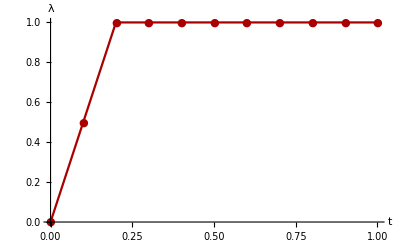

```mathematica
T=0.2;
λf[t_]:=If[t<T,t/T,1];
ListLinePlot[Table[{t,λf[t]},{t,0,1,0.1}],AxesLabel->{"t","λ"},PlotStyle->Darker[Red],PlotMarkers->"●",LabelStyle->Directive[FontSize->16,FontFamily->"Times",Black],PlotRange->All]
```

```mathematica
tMax=1.;t0=tMax/10.;ΔtMin=tMax/100.;ΔtMax=tMax/10.;
tolNR=10^-8;maxNR=50;targetNR=8;
tu={{0,0}};
xc={};

tMax=1;
nstep=10;
t0=tMax/nstep;ΔtMin=t0/100;ΔtMax=t0;

SMTNextStep["t"->t0,"λ[t]"->λf];
While[
While[step=SMTConvergence[tolNR,maxNR,{"Adaptive Time",targetNR,ΔtMin,ΔtMax,tMax}], SMTNewtonIteration[];];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧,SMTStepBack[];
, (*Postprocessing*)
tu=AppendTo[tu,{SMTData["Time"],SMTPostData["u",Point[{ri,0}]]}];
xc=AppendTo[xc,Table[{ri+i δ,SMTPostData["c",Point[{ri+i δ,0}]]},{i,0,1,0.1}]];
];
SMTNextStep["Δt"->step⟦2⟧,"λ[t]"->λf]
];
tu=AppendTo[tu,{SMTData["Time"],SMTPostData["u",Point[{ri,0}]]}];
xc=AppendTo[xc,Table[{ri+i δ,SMTPostData["c",Point[{ri+i δ,0}]]},{i,0,1,0.1}]];
```

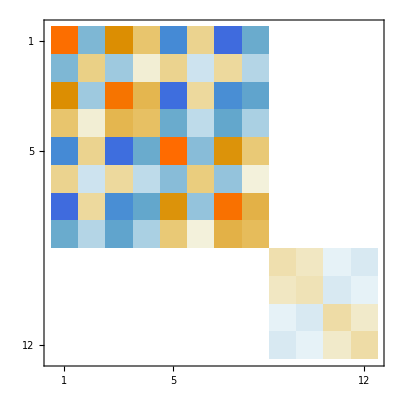

```mathematica
SMTData[1,"SKR"]⟦1⟧//MatrixPlot
```

### Results

```mathematica
SMTShowMesh["BoundaryConditions"->True,ImageSize->300]
```

-Graphics-

```mathematica
Show[SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,ImageSize->300],SMTShowMesh["Field"->"c","DeformedMesh"->True,ImageSize->300]]
```

-Graphics-

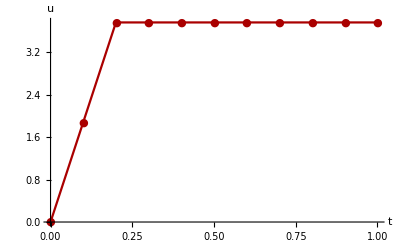

```mathematica
plot1=ListLinePlot[tu,AxesLabel->{"t","u"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

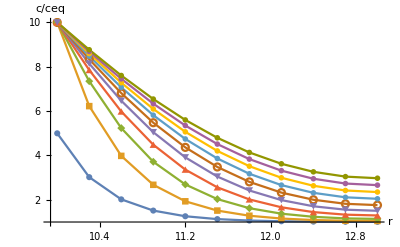

```mathematica
plot2=ListLinePlot[xc,AxesLabel->{"r","c/ceq"},PlotMarkers->Automatic,LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{All,{1,All}}]
```

## Punch test (for poroelastic applications)

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
SetupSimulation[pressure_]:=(
L=10;  H=3; q=50;
Kdr=100; G=50;
kp=10^-2;
M=1000;
α=0.75;
points={{0,0},{L,0},{L,H},{0,H}};

<<AceFEM`;
SMTInputData[];
SMTAddDomain["Ωc","Q1PElin",{"Kdr *"-> Kdr,"G *"->G,"kp *"->kp,"M *"->M,"α *"->α}];
SMTAddMesh[Polygon[points],"Ωc","Q1",{5L,5H}];

SMTAddEssentialBoundary[{Line[{{0,0},{L,0}},"D"],1-> 0, 2-> 0}];
SMTAddNaturalBoundary[Line[{{L/3,H},{2L/3,H}},"D"],2->Line[{-q}]];
SMTAddInitialBoundary["p",1->0,"Type"->"InitialCondition"];

(*For specifying drained conditions on the bottom side*)
SMTAddEssentialBoundary[{Line[{{0,0},{L,0}},"p"],1-> Line[{pressure}]}];

(*For uncoupled simulation: null pressure everywhere*)
(*SMTAddEssentialBoundary["p",1-> 0];*)

SMTAnalysis[];
);
```

### Solution algorithm (adaptive time-step, NR loop) - WITH POSTPROCESSING

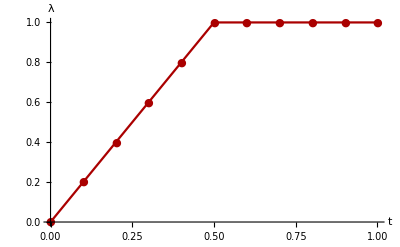

```mathematica
T=0.5;
λf[t_]:=If[t<T,t/T,1];ListLinePlot[Table[{t,λf[t]},{t,0,1,0.1}],AxesLabel->{"t","λ"},PlotStyle->Darker[Red],PlotMarkers->"●",LabelStyle->Directive[FontSize->16,FontFamily->"Times",Black],PlotRange->All]
```

```mathematica
SolveSimulation[]:=(
tolNR=10^-8;maxNR=50; targetNR=8;
tv={{0,0}};
tp={{0,0}};
T=0.5;
λf[t_]:=If[t<T,t/T,1];ListLinePlot[Table[{t,λf[t]},{t,0,1,0.1}],AxesLabel->{"t","λ"},PlotStyle->Darker[Red],PlotMarkers->"●",LabelStyle->Directive[FontSize->16,FontFamily->"Times",Black],PlotRange->All]
tMax=1;
nstep=10;
t0=tMax/nstep;ΔtMin=t0/100;ΔtMax=t0;
SMTAnimationOfResponse["Initialize"]
SMTNextStep["t"->t0,"λ[t]"->λf];
While[
While[step=SMTConvergence[tolNR,maxNR,{"Adaptive Time",targetNR,ΔtMin,ΔtMax,tMax}], SMTNewtonIteration[];];
If[Not[step⟦1⟧],SMTAnimationOfResponse["x"-> Hold[SMTData["Time"]] ,"y"->Hold[Total[ SMTPostData["p",Point[{L/2,H/2}]]]],"LeadingNodePosition"->{L/2,H/2},"ImageSize"->600,"Show"->"Window"|{"ExportFrames","responseFile"},"PlotOptions"->{PlotLabel->Subscript["p","center"]},"ShowMeshOptions"->{"Field"->"p","BoundaryConditions"->False},"Data"->Hold[{{SMTData["Time"],Total[ SMTPostData["p",Point[{L/2,H/2}]]]},{SMTData["Time"],Total[ SMTPostData["v",Point[{L/2,H}]]]}}]]];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧,SMTStepBack[];
, (*Postprocessing*)
tv=AppendTo[tv,{SMTData["Time"],SMTPostData["v",Point[{L/2,H}]]}];
tp=AppendTo[tp,{SMTData["Time"],SMTPostData["p",Point[{L/2,H/2}]]}];
];
SMTNextStep["Δt"->step⟦2⟧,"λ[t]"->λf]
];
 (*Postprocessing*)
tv=AppendTo[tv,{SMTData["Time"],SMTPostData["v",Point[{L/2,H}]]}];
tp=AppendTo[tp,{SMTData["Time"],SMTPostData["p",Point[{L/2,H/2}]]}];
Print[Show[GraphicsRow[{ListLinePlot[SMTAnimationOfResponse["Additional data"]⟦All,1⟧,PlotLabel->"p"],ListLinePlot[SMTAnimationOfResponse["Additional data"]⟦All,2⟧,PlotLabel->"v (L/2,H)"]},ImageSize->600]]];
Return[{SMTAnimationOfResponse["Additional data"]⟦All,1⟧,SMTAnimationOfResponse["Additional data"]⟦All,2⟧}]
)
```

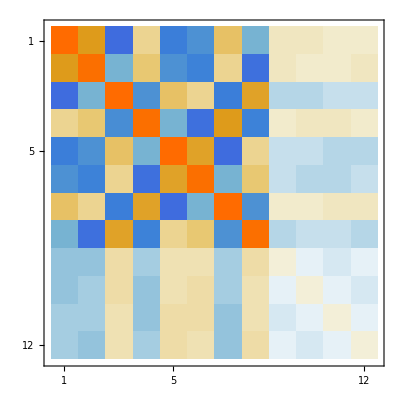

```mathematica
SMTData[1,"SKR"]⟦1⟧//MatrixPlot
```

### Results

```mathematica
Show[SMTShowMesh["FillElements"->False,ImageSize->400],SMTShowMesh["Field"->"v","DeformedMesh"->True,ImageSize->400]]
```

-Graphics-

```mathematica
Show[SMTShowMesh["FillElements"->False,ImageSize->400],SMTShowMesh["Field"->"p","DeformedMesh"->True,ImageSize->400]]
```

-Graphics-

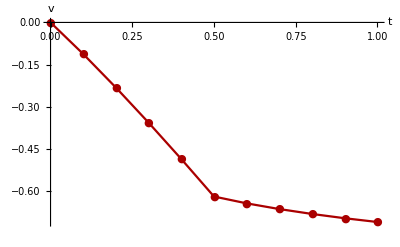

```mathematica
ListLinePlot[tv,AxesLabel->{"t","v"},PlotStyle->Darker[Red],PlotMarkers->"●",LabelStyle->Directive[FontSize->16,FontFamily->"Times",Black]]
```

```mathematica
ListLinePlot[tp,AxesLabel->{"t","p"},PlotStyle->Darker[Red],PlotMarkers->"●",LabelStyle->Directive[FontSize->16,FontFamily->"Times",Black]]
```

## Total simulation

```mathematica
<<AceFEM`;
```

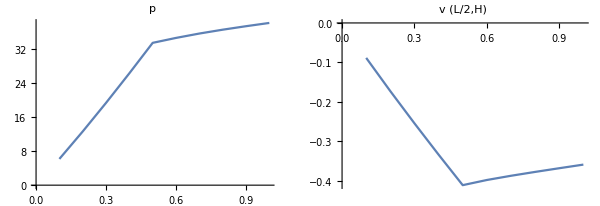

```mathematica
myPressure={};
myDisplacement={};
SetupSimulation[+300];
{myPressure,myDisplacement}=SolveSimulation[];
```

```mathematica
SMTAnimationOfResponse["Animate"]
```

```mathematica
Show[SMTShowMesh["FillElements"->True,"BoundaryConditions"->True,ImageSize->400,"DeformedMesh"->True]]
```

-Graphics-